```mathematica
(* For Exporting *)
SetDirectory[NotebookDirectory[]];

bin=Databin["66W7CW2x"];

(* Take the arbitrary number stored and convert it to a DaetObject, then a string *)
times=Normal[DateString/@(DateObject/@Dataset[bin][All,"Timestamp"])];
(* Use the names from the last row to be sure to have them all *)
names=Select[Keys[Dataset[bin][Length[Dataset[bin]]]]//Normal,StringContainsQ[#,"("]&];
Clear[data]
data=ToExpression[names/.(Dataset[bin][All,names]//Normal)];
dayTimes=N[(AbsoluteTime[#]-AbsoluteTime[times[[Length[times]]]])/(3600*24)]&/@times;

(* This may not work when a new candidate is added now... *)
InvalidNum=-1;
data=Module[{emptyData},

emptyData=Table[Table[

If[Or[Length[data[[j]]]<i,
StringLength[ToString[data[[j,i]]]]==0],
InvalidNum,data[[j,i]]]

,{i,Length[names]}],{j,Length[data]}]];
(* This one will be better... *)
MissingIndices[name_String]:=Union[Flatten[Position[MissingQ/@Dataset[bin][All,name],True]]]

lastNamesWithParty=Module[{split},(split=StringSplit[#];StringJoin[split[[2]]," ",split[[3]]])&/@names];
lastNamesWithoutParty=Module[{split},(split=StringSplit[#];split[[2]])&/@names];

(* A function that finds the indices of all elements of a list of strings that contain a particular substring. *)
GetIndicesFromList[list_List,str_String]:=Module[{vals},
vals=Select[list,StringContainsQ[#,str]&];
Flatten[Union[Position[list,#]&/@vals]
]]
(* Republican and Democrat indices. *)
reps=GetIndicesFromList[names,"(R)"];
dems=GetIndicesFromList[names,"(D)"];
(* convert a data set where each row of data was taken at the same time *)
ConvertToTimes[data_List,times_List]:=If[Length[data]≠Length[times],Message[ConvertToTimes::illegal],
Table[TimeSeries[Table[{times[[i]],data[[i,j]]},{i,Length[times]}]],{j,Length[data[[1]]]}]]
absoluteDiffData=Differences[data];
percentDiffData=absoluteDiffData/data[[1;;Length[data]-1]]//N;
titles={"Total Likes","Overnight Change (Absolute)","Overnight Change (Percentage)"};
pieTitles={"Total Likes (#)","Total Likes (%)","Overnight Change (#)","Overnight Change (%)"};
findIndex[candidate_String]:=Position[names,_String?(StringContainsQ[#,candidate]&)][[1,1]]

graphFn[option_Integer,selection_List,scale_Integer,customStyle_List:{RGBColor[0., 0.0016329999999999956, 0.565225],RGBColor[0., 0.07322799999999996, 0.848096],RGBColor[0., 0.6, 0.6],RGBColor[0.04072600000000004, 0.38550399999999996, 0.533684],RGBColor[0.09955000000000003, 0.9795987, 0.9698177],RGBColor[0.17006200000000005, 0.27484600000000003, 0.],RGBColor[0.20956699999999995, 0.549706, 0.],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[0.4, 0.8, 1],RGBColor[0.436362, 0.393744, 0.06414900000000001],RGBColor[0.45412399999999997, 0., 0.441245],RGBColor[0.501961, 0, 0.25098],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.566842, 0.967407, 1],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0.698817, 0.873304, 0.295247],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[0.7268939999999999, 0.45700799999999997, 0.504417],RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0.927596, 0.725414, 0.204257],RGBColor[1, 0.998367, 0.434775]},plotRange_:All]:=Module[
{labels,plotLabel,graph,graphTimes,fn,styles},
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
plotLabel=titles[[option]];
graph=If[option==1,data,If[option==2,absoluteDiffData,percentDiffData*100]];
graphTimes=If[option==1,times,times[[2;;]]];
fn=If[scale==1,DateListPlot,DateListLogPlot];
styles=customStyle;

fn[ConvertToTimes[graph[[All,selection]],graphTimes],PlotLegends->labels[[selection]],
PlotLabel->plotLabel,
PlotRange->plotRange,
PlotStyle->styles]]

pieFn[option_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,graphTimes,totalLikes,labelfn,ts},
plotLabel=pieTitles[[option]];
graph=If[option≤2,data,If[option==3,absoluteDiffData,percentDiffData//N]];
graphTimes=If[option≤2,times,times[[2;;]]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
ts=Min[timestamp,Length[graphTimes]];
totalLikes=Total[graph[[ts,selection]]];
labelfn=If[option==1,(Placed[Row[{NumberForm[IntegerPart[#/1000],DigitBlock->3],"k"}],"RadialCenter"]&),

If[option==3,
(Placed[Row[{NumberForm[IntegerPart[#],DigitBlock->3],""}],"RadialCenter"]&),

If[option==2,(Placed[Row[{N[#/totalLikes,3]*100,"%"}],"RadialCenter"]&),
(Placed[Row[{N[#,3]*100,"%"}],"RadialCenter"]&)
]]];

PieChart[graph[[ts,selection]],ChartLabels->Placed[labels[[selection]],"RadialCallout"],PlotLabel->plotLabel<>"\n"<>graphTimes[[ts]],
LabelingFunction->labelfn
]]

tableFn[sort_Integer,order_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,tableData,ordering},
plotLabel=titles[[sort]];
graph=If[sort==1,data,If[sort==2,absoluteDiffData,percentDiffData//N]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
tableData=Table[{data[[timestamp+1,i]],absoluteDiffData[[timestamp,i]],
percentDiffData[[timestamp,i]],
ToString[percentDiffData[[timestamp,i]]*100]<>"%"},{i,selection}];
ordering=If[sort==0,
Ordering[labels[[selection]]],
Ordering[tableData,All,#1[[sort]]>#2[[sort]]&]];
ordering=If[order==1,ordering,Reverse[ordering]];

Labeled[TableForm[tableData[[ordering,{1,2,4}]],TableHeadings->{labels[[selection[[ordering]]]],{"Total Likes","Overnight Gains\n(Absolute)","Overnight Gains\n(Percentage)"}}],"Likes as of "<>times[[timestamp+1]]<>"\n",Top]]
(*NewCandidate[names,times,data,"like_data.csv"]*)



(* FIXME : Need a new replacement for the NewCandidate -- base it on the MissingIndices function? *)
```

ToExpression::notstrbox: Missing["KeyAbsent", "John Kasich (R)"] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

```mathematica
Manipulate[
graphFn[option,selection,scale],
{{option,1},
(#->titles[[#]])&/@Range[Length[titles]]},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}},
{{scale,1},{1->"Normal",2->"Log"}}
]
```

```mathematica
Manipulate[
pieFn[option,timestamp,selection],

{{option,1},
(#->pieTitles[[#]]&/@Range[Length[pieTitles]])},
{timestamp,1,Length[times],1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
CloudDeploy[%269,Permissions->"Public"]
```

CloudObject[]

```mathematica
Manipulate[tableFn[sort,order,timestamp,selection],
{{sort,1},
Union[(#->titles[[#]])&/@Range[Length[titles]],{0->"Name"}]},
{{order,1},{1->"Descending",2->"Ascending"}},
{timestamp,1,Length[times]-1,1},
{{selection,Range[1,Length[names[[1;;21]]]]},{Range[1,Length[names[[1;;21]]]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
Export["table.png",tableFn[3,1,35,Range[Length[names]-1]],ImageResolution->400]
```

table.png

```mathematica
CloudDeploy[%271,Permissions->"Public"]
```

CloudObject[]

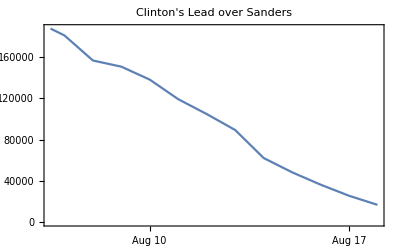

{{x→0.575795}}

```mathematica
DateListPlot[Table[{times[[i]],data[[i,findIndex["Clinton"]]]-data[[i,findIndex["Sanders"]]]},{i,35,Length[data]}],PlotLabel->"Clinton's Lead over Sanders"]
(* FIXME: Make this based on time, not index -- some days aren't at the same time*)
Solve[LinearModelFit[{dayTimes[[35;;]],data[[35;;,findIndex["Clinton"]]]-data[[35;;,findIndex["Sanders"]]]}//Transpose,{x},x]["BestFit"]==0,x]
```

```mathematica
Solve[LinearModelFit[{dayTimes[[1;;]],data[[1;;,findIndex["Clinton"]]]-data[[1;;,findIndex["Sanders"]]]}//Transpose,{x},x]["BestFit"]==0,x]
```

{{x→42.9519}}

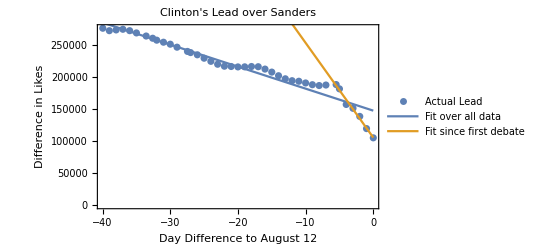

```mathematica
Show[ListPlot[{dayTimes,data[[All,findIndex["Clinton"]]]-data[[All,findIndex["Sanders"]]]}//Transpose,
PlotLegends->{"Actual Lead"}],
Plot[{Normal[LinearModelFit[{dayTimes[[;;]],data[[;;,findIndex["Clinton"]]]-data[[;;,findIndex["Sanders"]]]}//Transpose,{x},x]]/.{x->t},
Normal[LinearModelFit[{dayTimes[[35;;]],data[[35;;,findIndex["Clinton"]]]-data[[35;;,findIndex["Sanders"]]]}//Transpose,{x},x]]/.{x->t}},{t,-Length[data],0},
PlotLegends->{"Fit over all data","Fit since first debate"}],
PlotLabel->"Clinton's Lead over Sanders",
FrameLabel->{"Day Difference to August 12","Difference in Likes"},
Frame->True
]
```

```mathematica
((#[[1]])/#[[2]]//N)&/@percentDiffData[[All,{findIndex["Sanders"],findIndex["Clinton"]}]]
```

{2.81561,1.13268,1.13681,1.97213,2.59463,2.65418,2.68433,3.00363,2.82221,2.65728,2.80926,2.05777,2.16439,2.45424,2.96975,3.38932,3.09057,2.3433,1.37053,1.49049,1.20241,1.04448,1.37509,2.89527,3.94649,3.52474,3.21272}

```mathematica
Manipulate[
Quiet[Quiet[
Labeled[TableForm[Sort[{lastNamesWithParty[[#]],(LinearModelFit[({dayTimes[[35;;]],data[[35;;,#]]}//Transpose),{x},x]["BestFit"]/.{x->time})}&/@(findIndex/@lastNamesWithoutParty[[1;;21]]),#1[[2]]>#2[[2]]&]],
"Estimated Total Likes from Linear Fit\n"<>DatePlus[times[[Length[times]]],time]
,Top]],{Part::pkspec1}],{time,1,QuantityMagnitude[DateDifference[Today,DateObject[{2016,11,8}]]],1}]
```

```mathematica
CloudDeploy[%294,Permissions->"Public"]
```

CloudObject[]

```mathematica
(*SetDirectory[NotebookDirectory[]];
data2=Import["like_data.csv"];
bin=Databin["66W7CW2x"];
names=data2[[1]];
data2=data2[[2;;]];
InvalidNum=-1;
emptyData=Table[Table[

If[Or[Length[data2[[j]]]<i,
StringLength[ToString[data2[[j,i]]]]==0],
InvalidNum,data2[[j,i]]]

,{i,Length[names]}],{j,Length[data2]}];
data2=emptyData;

(* Add literally everything *)
For[i=1,i≤Length[data2],i++,DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data2[[i,1;;Length[names]]]}]]]]
(*  THIS IS THE IMPORTANT ONE -- HOW TO ADD IN CASE OF ERROR   *)
data2=Import["like_data.csv"];
names=data2[[1]];
DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data2[[Length[data2],1;;Length[names]]]}]]]


times=(DateObject/@Dataset[bin][All,"Timestamp"]);*)
(*ResetTheDatabin[]:=For[i=0,i<Length[data],i++,DatabinRemove[bin,1]]*)
(*For[i=1,i≤Length[data],i++,DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data[[i]]}]]]]*)
```

```mathematica
RandomSample[Flatten[{#,ColorNegate[#]}&/@Flatten[MapThread[{#1,#2}&,{(*Table[ColorData["VisibleSpectrum"][410+(i/22)^1*(720-410)],{i,1,21,1}],*)ColorData[60,"ColorList"],ColorData[54,"ColorList"]}]]],22]
```

{RGBColor[0.927596, 0.725414, 0.204257],RGBColor[0., 0.6, 0.6],RGBColor[0.04072600000000004, 0.38550399999999996, 0.533684],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0.436362, 0.393744, 0.06414900000000001],RGBColor[0.17006200000000005, 0.27484600000000003, 0.],RGBColor[0.501961, 0, 0.25098],RGBColor[0.698817, 0.873304, 0.295247],RGBColor[0.09955000000000003, 0.9795987, 0.9698177],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[1, 0.998367, 0.434775],RGBColor[0.45412399999999997, 0., 0.441245],RGBColor[0., 0.07322799999999996, 0.848096],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0., 0.0016329999999999956, 0.565225],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[0.7268939999999999, 0.45700799999999997, 0.504417],RGBColor[0.566842, 0.967407, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.4, 0.8, 1],RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.20956699999999995, 0.549706, 0.]}

```mathematica
Module[{m},m=Sort[{#,100(data[[Length[data],findIndex[#]]]/data[[1,findIndex[#]]]-1)//N,data[[Length[data],findIndex[#]]]}&/@lastNamesWithParty[[1;;21]],#1[[2]]>#2[[2]]&];
Labeled[TableForm[{"+"<>ToString[#[[1]]]<>"%",#[[2]]}&/@m[[All,{2,3}]],TableHeadings->{m[[All,1]],{"Percent Change","Total Likes"}}],"Percent change since July 3",Top]]
```

| Percent Change | Total Likes
Fiorina (R) | +172.74% | 267182
Sanders (D) | +60.2343% | 1157393
Trump (R) | +56.4786% | 3166797
Carson (R) | +43.7701% | 2345899
Webb (D) | +24.1732% | 30225
Bush (R) | +18.2433% | 248694
Clinton (D) | +17.6679% | 1174184
Pataki (R) | +13.0045% | 18283
Chafee (D) | +11.3151% | 8854
Graham (R) | +9.33443% | 129265
Cruz (R) | +8.56737% | 1371701
Christie (R) | +7.81206% | 118700
Rubio (R) | +7.69479% | 973044
Jindal (R) | +6.82522% | 276328
O'Malley (D) | +5.0171% | 76443
Walker (R) | +3.75096% | 292669
Huckabee (R) | +3.07222% | 1825209
Paul (R) | +1.61858% | 2059204
Perry (R) | +0.945835% | 1209000
Santorum (R) | +0.726985% | 264639
Biden (D) | +0.573371% | 840375Percent change since July 3